# RetargetCircuit

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Deprecation

Renamed to GetCircuitRetargeted as of v0.18

```mathematica
?RetargetCircuit
```

```mathematica
RetargetCircuit[Subscript[X, 2], 2->1]
```

GetCircuitRetargeted::error: The function RetargetCircuit[] is deprecated, though has still been attemptedly performed. In future, please use GetCircuitRetargeted[], or temporarily hide this message using Quiet[].

{X_1}

```mathematica
?GetCircuitRetargeted
```

## Doc

```mathematica
?RetargetCircuit
```

## Tests

```mathematica
?QuEST`Gate`*
```

### Arbitrary rules

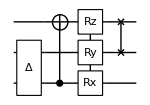

```mathematica
in = Circuit[Subscript[Depol, 0,1][x] Subscript[C, 0][Subscript[X, 2]] R[x,Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]] Subscript[SWAP, 1,2]];
DrawCircuit[in]
```

{Depol_(2,1)[x],C_2[X_0],R[x,X_2 Y_1 Z_0],SWAP_(1,0)}

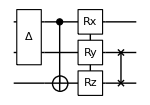

```mathematica
out = RetargetCircuit[in, {0->2,2->0}]
DrawCircuit[out]
```

{Depol_(1,2)[x],C_1[X_3],R[x,X_1 Y_2 Z_3],SWAP_(2,3)}

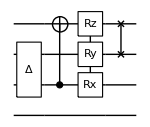

```mathematica
out = RetargetCircuit[in, q_ -> q+1]
DrawCircuit[out]
```

### Gate support, and no modification of arguments

```mathematica
RetargetCircuit[ Circuit[
	Subscript[Damp, 0][0] Subscript[Deph, 0,1][0] Subscript[Depol, 0,1][0] Fac[0] G[0] Subscript[H, 0] Subscript[Id, 0,1]
	Subscript[Kraus, 0,1][0,0] Subscript[KrausNonTP, 0,1][0,1] Subscript[M, 0,1] Subscript[Matr, 0,1][0]
	Subscript[P, 0,1][0,1] Subscript[Ph, 0,1][0] R[0, Subscript[X, 0]] R[0,Subscript[X, 0] Subscript[Y, 0] Subscript[Z, 1]] Subscript[Rx, 0,1][0]
	Subscript[Ry, 0,1][0] Subscript[Rz, 0,1][0] Subscript[S, 0] Subscript[SWAP, 0,1] Subscript[T, 0] Subscript[U, 0,1][0,1]
	Subscript[UNonNorm, 0,1][0,1] Subscript[X, 0] Subscript[Y, 0] Subscript[Z, 0]],
	0->a]
```

{Damp_a[0],Deph_(a,1)[0],Depol_(a,1)[0],Fac[0],G[0],H_a,Id_(a,1),Kraus_(a,1)[0,0],KrausNonTP_(a,1)[0,1],M_(a,1),Matr_(a,1)[0],P_(a,1)[0,1],Ph_(a,1)[0],R[0,X_a],R[0,X_a Y_a Z_1],Rx_(a,1)[0],Ry_(a,1)[0],Rz_(a,1)[0],S_a,SWAP_(a,1),T_a,U_(a,1)[0,1],UNonNorm_(a,1)[0,1],X_a,Y_a,Z_a}

### Controls

```mathematica
RetargetCircuit[Subscript[C, 0,1,2][Subscript[X, 3]], {0->a, 3->b}]
```

{C_(a,1,2)[X_b]}

### Qubit configurations (sequence vs list)

```mathematica
RetargetCircuit[{Subscript[X, 0], Subscript[X, 0,1], Subscript[X, {0}], Subscript[X, {0,1}]},  0->a]
```

{X_a,X_(a,1),X_{a},X_{a,1}}

```mathematica
RetargetCircuit[{Subscript[Ph, 0][0], Subscript[Ph, 0,1][0], Subscript[Ph, {0}][0], Subscript[Ph, {0,1}][0]},  0->a]
```

{Ph_a[0],Ph_(a,1)[0],Ph_{a}[0],Ph_{a,1}[0]}

```mathematica
RetargetCircuit[{R[0,Subscript[X, 0]], R[0,Subscript[X, 0] Subscript[Y, 0] Subscript[Z, 1]]} , 0->a]
```

{R[0,X_a],R[0,X_a Y_a Z_1]}

```mathematica
RetargetCircuit[{Subscript[C, 0]@R[0,Subscript[X, 0]], Subscript[C, {0,1}]@R[0,Subscript[X, 0] Subscript[Y, 0] Subscript[Z, 1]]} , 0->a]
```

{C_a[R[0,X_a]],C_{a,1}[R[0,X_a Y_a Z_1]]}

### Non-integer qubits

```mathematica
RetargetCircuit[{Subscript[Rx, a][a]},  a->b]
```

{Rx_b[a]}

## Errors

```mathematica
RetargetCircuit[{Subscript[X, 0],Subscript[Y, 1]}, invalid]
```

ReplaceAll::reps: {invalid} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Failed

```mathematica
RetargetCircuit[{Anon}, 0->1]
```

RetargetCircuit::error: Could not identify qubits in unrecognised gate: Anon

$Failed

```mathematica
RetargetCircuit[hi]
```

RetargetCircuit::error: Invalid arguments. See ?RetargetCircuit

$Failed

```mathematica
RetargetCircuit[hello, there, friend]
```

RetargetCircuit::error: Invalid arguments. See ?RetargetCircuit

$Failed